```mathematica
ClearAll["Global`*"]
```

```mathematica
q=0.99;(*M2=QM1*)
MBH1=100;(*40 M_⊙, 1 M_⊙≈9.135*10^37 Subscript[M, pl]*)
α=0.06;(*fine structure constant*)
MCloud=0.1; (*total mass of the cloud*)

Num=200;(*evaluate Num points*)
xStart=10;(*start at R=10Rb1*)
xEnd=38;(*end at R=38Rb1*)
xValues=Subdivide[xStart,xEnd,Num-1];(*separations to evaluate*)

NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"GMCalcLib_v2.0.nb"}]];

FilePath=FileNameJoin[{NotebookDirectory[],"data"}];(*path to the storage folder*)
GMInitialize[q,MBH1,α,MCloud,FilePath]
(*If you want to do numerical calculations...
ComputeAndSaveIntegrands[]
ComputeAndSaveReducedHamiltonian[]
ComputeAndSaveXc[]
ComputeAndSaveQc[]*)
```

eigenvectors:

-Graphics-

eigenvalues:

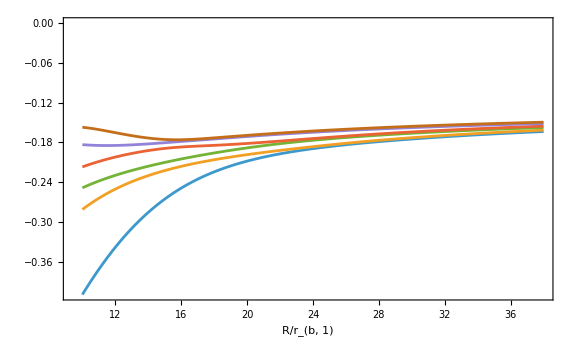

eigenvalue derivatives:

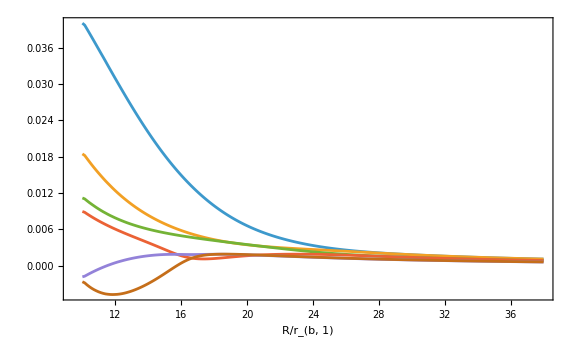

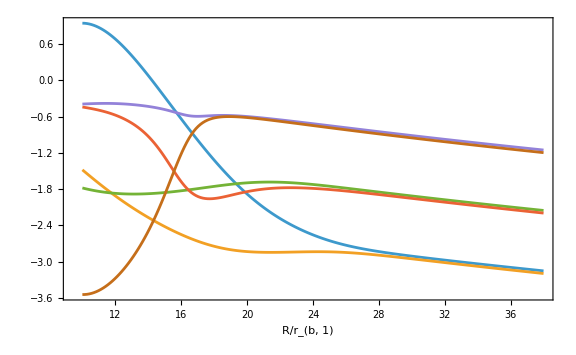

```mathematica
GetEigensystem[]

(*draw eigenvectors*)
eigenvectorsData={};
For[eigenvectorInd=1,eigenvectorInd<=6,eigenvectorInd++,
firstEigenvec=eigenvectors[[All,eigenvectorInd]];
correctedVecs=FoldList[Function[{prev,current},If[Dot[prev,current]<0,-current,current]],First[firstEigenvec],Rest[firstEigenvec]];
threshold=0.5;
smoothedComponents=Table[
component=correctedVecs[[All,i]];
Do[If[Abs[component[[j]]-component[[j-1]]]>threshold,component[[j;;]]=-component[[j;;]];Break[]],{j,2,Length[component]}];
component,{i,1,6}
];
CurrentEigenvectorsData={};
For[directionInd=1,directionInd<=6,directionInd++,
AppendTo[CurrentEigenvectorsData,Transpose[{xValues,smoothedComponents[[directionInd,All]]}]];
];
AppendTo[eigenvectorsData,CurrentEigenvectorsData];
];

Print["eigenvectors:"]
ResourceFunction["PlotGrid"][
{{ListLinePlot[eigenvectorsData[[1]],Frame->False,PlotRange->{-1.1,1.1},PlotLabel->"",LabelStyle->Directive[Black,FontSize->15]],ListLinePlot[eigenvectorsData[[2]],Frame->False,PlotRange->{-1.1,1.1},PlotLabel->"",LabelStyle->Directive[Black,FontSize->15]],ListLinePlot[eigenvectorsData[[3]],Frame->False,PlotRange->{-1.1,1.1},PlotLabel->"",LabelStyle->Directive[Black,FontSize->15]]},
{ListLinePlot[eigenvectorsData[[4]],Frame->False,PlotRange->{-1.1,1.1},PlotLabel->"",LabelStyle->Directive[Black,FontSize->15]],ListLinePlot[eigenvectorsData[[5]],Frame->False,PlotRange->{-1.1,1.1},PlotLabel->"",LabelStyle->Directive[Black,FontSize->15]],ListLinePlot[eigenvectorsData[[6]],Frame->False,PlotRange->{-1.1,1.1},PlotLabel->"",LabelStyle->Directive[Black,FontSize->15],PlotLegends->{"","","","","",""}]}},
ImageSize->1000,Spacings->20
]


EigenvaluesData=Transpose[{xValues,#}]&/@Transpose[eigenvalues/(μ α1^2)/.{α1->α,M1->M}];

Print["eigenvalues:"]
ListLinePlot[EigenvaluesData,FrameLabel->{"R/r_(b, 1)",""},Frame->True,ImageSize->Large,PlotRange->All,FrameStyle->Directive[Black,Times,20],PlotLegends->{"","","","","",""},Frame->True,LabelStyle->Directive[Black,FontSize->20]]

EigenvalueDerivativesData=Transpose[{xValues,#}]&/@Transpose[EigenvalueDerivatives/(μ α1^2)/.{α1->α,M1->M}];

Print["eigenvalue derivatives:"]
ListLinePlot[EigenvalueDerivativesData,FrameLabel->{"R/r_(b, 1)",""},Frame->True,ImageSize->Large,PlotRange->All,PlotLegends->{"","","","","",""},Frame->True,LabelStyle->Directive[Black,FontSize->20]]

DHDΩOfEigenvectorData=Transpose[{xValues,#}]&/@Transpose[DHDΩOfEigenvector/.{α1->α,M1->M}];
ListLinePlot[DHDΩOfEigenvectorData,FrameLabel->{"R/r_(b, 1)",""},Frame->True,ImageSize->Large,PlotRange->All,PlotLegends->{"","","","","",""},Frame->True,LabelStyle->Directive[Black,FontSize->20]]
```

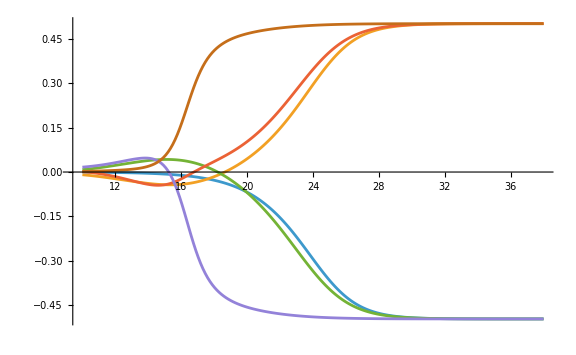

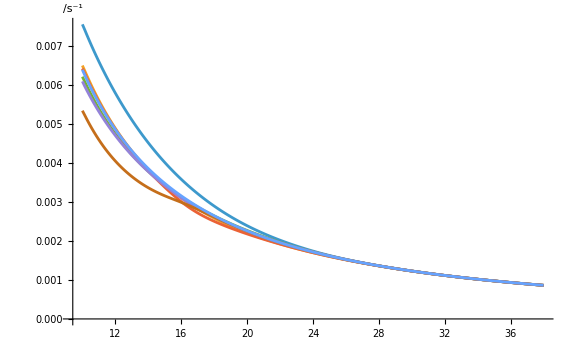

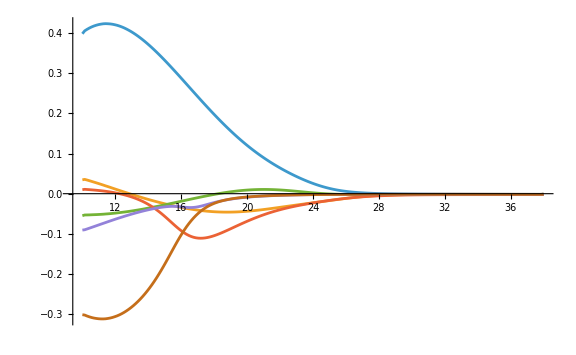

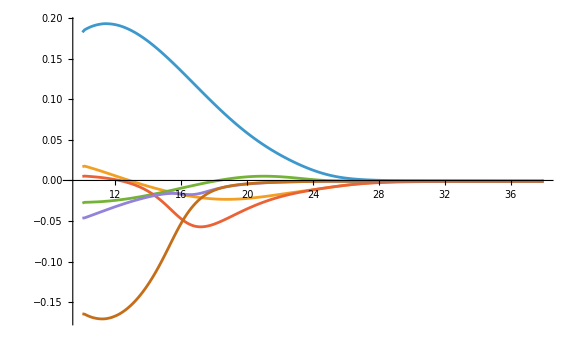

```mathematica
GetGWFreqSquare[];
For[i=1,i<=6,i++,
AppendTo[XcData,Transpose[{xValues,Xcs[[i]]/xValues}]];
AppendTo[RotationFreqForAllData,Transpose[{xValues,Sqrt[GWFreqSquare[[i]]]/Tpl/.{M1->M,α1->α,Q->q}}]];
AppendTo[RotationFreqSquareDeviationForAllData,Transpose[{xValues,π^2*GWFreqSquare[[i]]/((M1+M2+Mc)/(xValues^3*Rb1^3))-1/.{M1->M,α1->α,Q->q}}]];
AppendTo[RotationFreqDeviationForAllData,Transpose[{xValues,π*Sqrt[GWFreqSquare[[i]]]/(Sqrt[(M1+M2+Mc)/(xValues^3*Rb1^3)])-1/.{M1->M,α1->α,Q->q}}]];
]

AppendTo[RotationFreqForAllData,Transpose[{xValues,1/π Sqrt[(M1+M2+Mc)/(xValues^3*Rb1^3)]/Tpl/.{M1->M,α1->α,Q->q}}]];

ListLinePlot[XcData,AxesLabel->{"",""},ImageSize->Large,PlotLegends->{"","","","","",""},LabelStyle->Directive[Black,FontSize->20]]
ListLinePlot[RotationFreqForAllData,AxesLabel->{"","/s^-1"},ImageSize->Large,PlotLegends->{"","","","","","",""},LabelStyle->Directive[Black,FontSize->20]]
ListLinePlot[RotationFreqSquareDeviationForAllData,AxesLabel->{"",""},ImageSize->Large,PlotLegends->{"","","","","",""},PlotRange->All,LabelStyle->Directive[Black,FontSize->20]]
ListLinePlot[RotationFreqDeviationForAllData,AxesLabel->{"",""},ImageSize->Large,PlotLegends->{"","","","","",""},PlotRange->All,LabelStyle->Directive[Black,FontSize->20]]
```

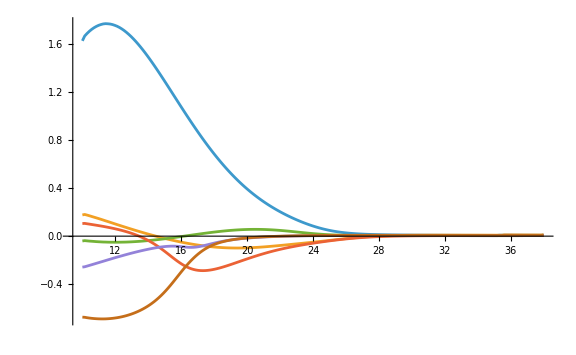

```mathematica
GetGRPower[]

GRPowerDeviationForAllData={};

For[i=1,i<=6,i++,
OriginalGRPower=If[i<=3,
32/5*((M1+Mc)^2 M2^2(M1+M2+Mc))/(xValues*Rb1)^5/.{M1->M,α1->α,Q->q},
32/5*(M1^2(M2+Mc)^2(M1+M2+Mc))/(xValues*Rb1)^5/.{M1->M,α1->α,Q->q}
];
AppendTo[GRPowerDeviationForAllData,Transpose[{xValues,GRPower[[i]]/OriginalGRPower-1}]];
]

ListLinePlot[GRPowerDeviationForAllData,AxesLabel->{"",""},ImageSize->Large,PlotLegends->{"","","","","",""},LabelStyle->Directive[Black,FontSize->20],PlotRange->All]
```

energies in lab frame:

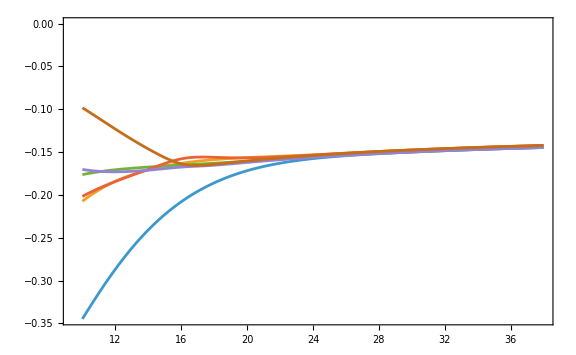

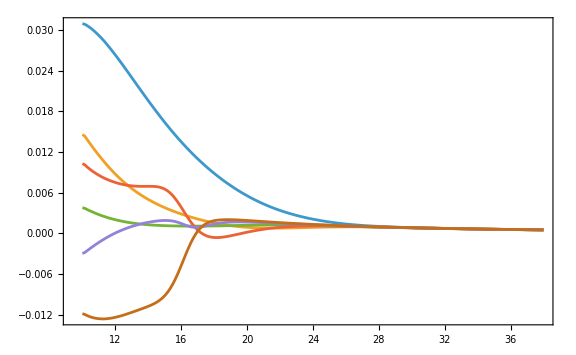

energy in lab derivatives:

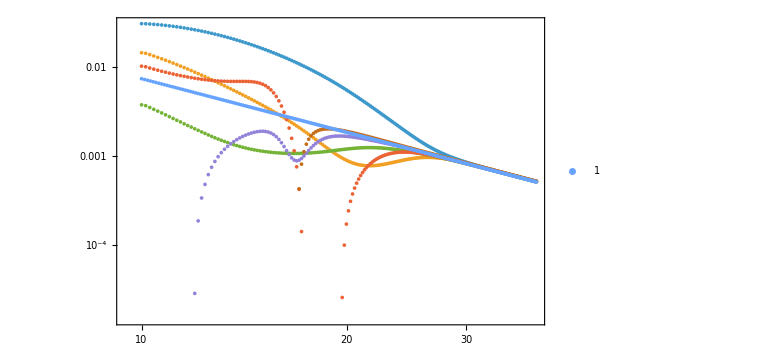

-Graphics-

energy in lab derivatives:

-Graphics-

```mathematica
GetCloudEnergiesInLab[];

CloudEnergiesInLabData=Transpose[{xValues,#}]&/@Transpose[CloudEnergiesInLab/(μ α1^2)/.{α1->α,M1->M}];

Print["energies in lab frame:"]
ListLinePlot[CloudEnergiesInLabData,FrameLabel->{"",""},Frame->True,ImageSize->Large,PlotRange->All,PlotLegends->{"","","","","",""},Frame->True,LabelStyle->Directive[Black,FontSize->20]]

CloudEnergyInLabDerivativesData=Transpose[{xValues,#}]&/@Transpose[CloudEnergyInLabDerivatives/(μ α1^2)/.{α1->α,M1->M}];
ListLinePlot[CloudEnergyInLabDerivativesData,FrameLabel->{"",""},Frame->True,ImageSize->Large,PlotRange->All,PlotLegends->{"","","","","","","1"},Frame->True,LabelStyle->Directive[Black,FontSize->20]]
AppendTo[CloudEnergyInLabDerivativesData,Table[{xValues,(Q(2+Q))/(2(xValues)^2(1+Q))/.{M1->M,α1->α,Q->q}},{xValues,10,38,0.1}]];
Print["energy in lab derivatives:"]
ListLogLogPlot[CloudEnergyInLabDerivativesData,FrameLabel->{"",""},Frame->True,ImageSize->Large,PlotRange->All,PlotLegends->{"","","","","","","1"},Frame->True,LabelStyle->Directive[Black,FontSize->20]]
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 1418.36 and t = 1418.37.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 1659.75 and t = 1659.79.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 1584.11 and t = 1584.14.

General::stop: Further output of NDSolve::evcvmit will be suppressed during this calculation.

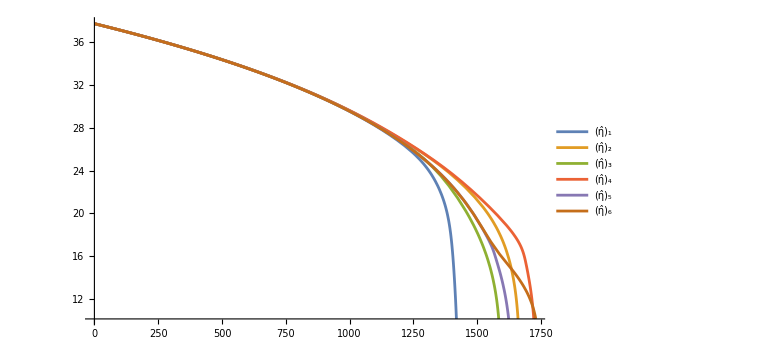

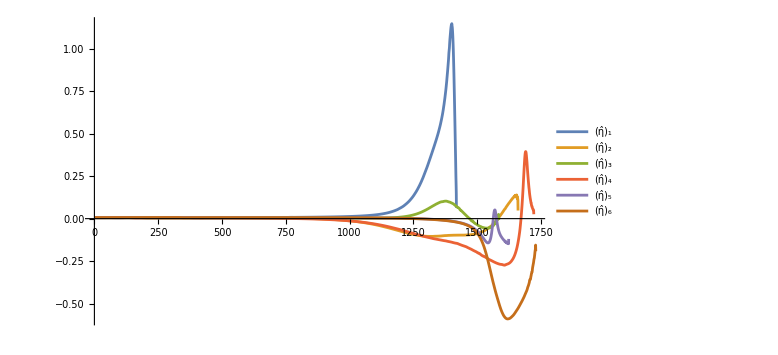

```mathematica
SysEnergiesInLab[eigenvectorIndex_]:=Module[{ρ1Values,ρ2Values,Xsys,d1,d2,CurrentEnergiesInLab},
ρ1Values=M2/(M1+M2)*xValues/.{M1->M,Q->q};
ρ2Values=M1/(M1+M2)*xValues/.{M1->M,Q->q};
Xsys=(Mc*Xcs[[eigenvectorIndex]]+M1*(-ρ1Values)+M2*ρ2Values)/(Mc+M1+M2)/.{M1->M,Q->q};

d1=M2/(M1+M2)*xValues+Xsys;(*CoM to BH1*)
d2=M1/(M1+M2)*xValues-Xsys;(*CoM to BH2*)

CurrentEnergiesInLab=Mc/μ*CloudEnergiesInLab[[All,eigenvectorIndex]]-(M1 M2)/(xValues Rb1)+1/2 M1 (π^2*GWFreqSquare[[eigenvectorIndex]])(d1 Rb1)^2+1/2 M2(π^2*GWFreqSquare[[eigenvectorIndex]])(d2 Rb1)^2/.{M1->M,α1->α,Q->q}
]

RtPlots={};
ChirpMassPlots={};

For[i=1,i<=6,i++,

(*interpolating functions*)
PInterpolation=Interpolation[Transpose[{xValues/.{M1->M,α1->α,Q->q},GRPower[[i]]}]];
EInterpolation=Interpolation[Transpose[{xValues/.{M1->M,α1->α,Q->q},SysEnergiesInLab[i]}]];
dEdR=Derivative[1][EInterpolation];

(*solve energy conservation equation*)
diffEq=dEdR[R[t]]*R'[t]/yrpl==-PInterpolation[R[t]];
R0=xValues[[Num-2]]/.{M1->M,α1->α,Q->q};
sol=NDSolve[{diffEq,R[0]==R0,WhenEvent[R[t]<=xValues[[2]]/. {M1->M,α1->α,Q->q},"StopIntegration"]},R,{t,0,Infinity},AccuracyGoal->10,PrecisionGoal->15];
RInterpolation=R/. sol[[1]];

FreqInterpolation=Interpolation[Transpose[{xValues/.{M1->M,α1->α,Q->q},Sqrt[GWFreqSquare[[i]]]}]];
dFdR=Derivative[1][FreqInterpolation];
dRdt=Derivative[1][RInterpolation];
ChirpMassFunc=Function[t,(5/96 π^(-8/3)*FreqInterpolation[RInterpolation[t]]^(-11/3)*dFdR[RInterpolation[t]]*dRdt[t]/yrpl)^(3/5)/. {M1->M,α1->α,Q->q}];
ChirpMassConst=If[i<=3,((M1+Mc)M2)^(3/5)/(M1+M2+Mc)^(1/5)/.{M1->M,α1->α,Q->q},(M1(M2+Mc))^(3/5)/(M1+M2+Mc)^(1/5)/.{M1->M,α1->α,Q->q}];
(*plot*)
tstop=dRdt["Domain"][[1,2]];
AppendTo[RtPlots,Plot[RInterpolation[t],{t,0,tstop},PlotStyle->ColorData[97][i],PlotLegends->Placed[{ToExpression["\\hat{\\eta}_"<>ToString[i],TeXForm]},Right],PlotRange->All]];AppendTo[ChirpMassPlots,Plot[ChirpMassFunc[t]/ChirpMassConst-1/. {M1->M,α1->α,Q->q},{t,0,tstop},PlotStyle->ColorData[97][i],PlotLegends->Placed[{ToExpression["\\hat{\\eta}_"<>ToString[i],TeXForm]},Right],PlotRange->All]];
]

(*Origional1Rt[t_]:=(R0^4-256/5*(M1+Mc)M2(M1+M2+Mc)*t/Rb1^4)^(1/4)/.{M1->M,α1->α,Q->q};
Origional2Rt[t_]:=(R0^4-256/5*M1*(M2+Mc)(M1+M2+Mc)*t/Rb1^4)^(1/4)/.{M1->M,α1->α,Q->q};*)
Show[RtPlots,AxesLabel->{"",""},ImageSize->Large,LabelStyle->Directive[Black,FontSize->20],PlotRange->All]
Show[ChirpMassPlots,AxesLabel->{"",""},ImageSize->Large,LabelStyle->Directive[Black,FontSize->20],PlotRange->All]
```

real part of eigenvalues at a1=0.23649, a2=0.234193:

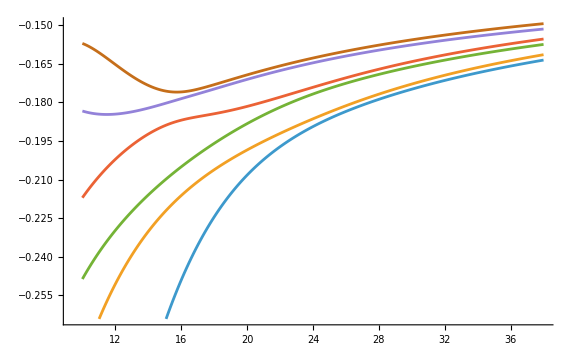

imaginary part (growth width) of eigenvalues at a1=0.23649, a2=0.234193:

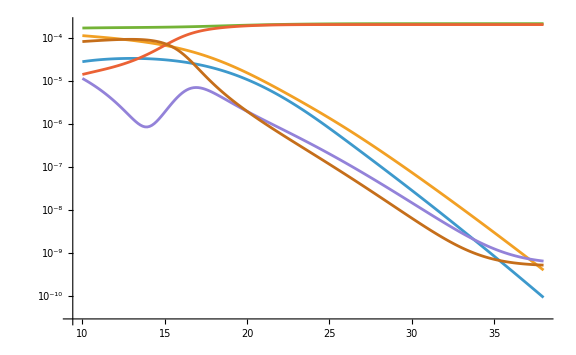

```mathematica
(*Subscript[ω, nlm]*)
LevelFrequncy[n_,α_]:=μ(1-α^2/(2 n^2));
(*growth width*)
GrowthWidth[{n_,l_,m_},a_,M_,α_]:=Module[{rplus,ΩH},
rplus=1+√(1-a^2);
ΩH=a/(2M rplus);(*This expression is wrong in paper Termination of Superradiance*)

2rplus (2^(4l+1)Factorial[n+l])/(n^(2l+4)Factorial[n-l-1])(Factorial[l]/(Factorial[2l]Factorial[2l+1]))^2 Product[k^2(1-a^2)+(a m-2rplus M LevelFrequncy[n,α])^2,{k,1,l}] (m ΩH-LevelFrequncy[n,α])α^(4l+5)
]

a1=1;
a2=1;

a1=x/.NSolve[m1 x/(2M1(1+√(1-x^2)))-LevelFrequncy[n1,α1]==0/.{n1->2,m1->1}/.{α1->α,M1->M,Q->q},x][[1]];(*a1 when 211,1 stops to grow*)
a2=x/.NSolve[m2 x/(2M2(1+√(1-x^2)))-LevelFrequncy[n2,α2]==0/.{n2->2,m2->1}/.{α1->α,M1->M,Q->q},x][[1]];(*a2 when 211,1 stops to grow*)

ReducedHamiltonian=DimlessReducedHamiltonian*(μ α1^2)/.{α1->α,M1->M,Q->q};

(*reduced Hamiltonian with non-Hermiticity added*)
ReducedHamiltonianWithGrowthWidth=Map[
ReplacePart[#,{
{1,1}->#[[1,1]]+ⅈ GrowthWidth[{2,0,0},a1,M1,α1],
{2,2}->#[[2,2]]+ⅈ GrowthWidth[{2,1,-1},a1,M1,α1],
{3,3}->#[[3,3]]+ⅈ GrowthWidth[{2,1,1},a1,M1,α1],
{4,4}->#[[4,4]]+ⅈ GrowthWidth[{2,0,0},a2,M2,α2],
{5,5}->#[[5,5]]+ⅈ GrowthWidth[{2,1,-1},a2,M2,α2],
{6,6}->#[[6,6]]+ⅈ GrowthWidth[{2,1,1},a2,M2,α2]
}]/.{α1->α,M1->M,Q->q}&,
ReducedHamiltonian
];

(*find eigensystem*)
{eigenvaluesWithGrowthWidth,eigenvectorsWithGrowthWidth}=Transpose[Map[Eigensystem,ReducedHamiltonianWithGrowthWidth]];

EigenvaluesWithGrowthWidthDataRe=Transpose[{xValues,#}]&/@Transpose[Re[eigenvaluesWithGrowthWidth]/(μ α1^2)/.{α1->α,M1->M,Q->q}];
EigenvaluesWithGrowthWidthDataIm=Transpose[{xValues,#}]&/@Transpose[Im[eigenvaluesWithGrowthWidth]/(μ α1^2)/.{α1->α,M1->M,Q->q}];

Log10EigenvaluesWithGrowthWidthDataIm=Transpose[{xValues,#}]&/@Transpose[Log10[Abs[Im[eigenvaluesWithGrowthWidth]]/(μ α1^2)]*Sign[Im[eigenvaluesWithGrowthWidth]]/.{α1->α,M1->M,Q->q}];

Print["real part of eigenvalues at a1=",a1,", a2=",a2,":"]
ListLinePlot[EigenvaluesWithGrowthWidthDataRe/.{α1->α,M1->M,Q->q},AxesLabel->{"",""},ImageSize->Large,PlotLegends->{"","","","","",""},LabelStyle->Directive[Black,FontSize->15]]

Print["imaginary part (growth width) of eigenvalues at a1=",a1,", a2=",a2,":"]
ListLinePlot[Abs[EigenvaluesWithGrowthWidthDataIm]/.{α1->α,M1->M,Q->q},AxesLabel->{"",""},ImageSize->Large,PlotLegends->{"","","","","",""},ScalingFunctions->{"Linear","Log10"},LabelStyle->Directive[Black,FontSize->15]]
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 1418.36 and t = 1418.37.

-Graphics-

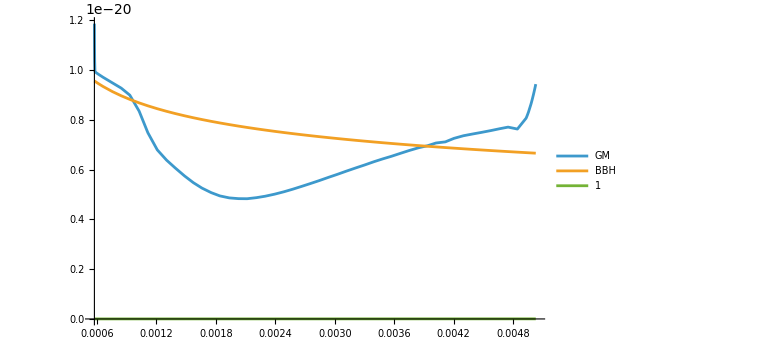

```mathematica
EigenvectorIndex=1;
PInterpolation=Interpolation[Transpose[{xValues/. {M1->M,α1->α,Q->q},GRPower[[EigenvectorIndex]]}]];
EInterpolation=Interpolation[Transpose[{xValues/. {M1->M,α1->α,Q->q},SysEnergiesInLab[EigenvectorIndex]}]];
dEdR=Derivative[1][EInterpolation];
(*定义微分方程*)diffEq=dEdR[R[t]]*R'[t]/yrpl==-PInterpolation[R[t]];
R0=xValues[[Num-2]]/. {M1->M,α1->α,Q->q};
sol=NDSolve[{diffEq,R[0]==R0,WhenEvent[R[t]<=xValues[[2]]/. {M1->M,α1->α,Q->q},"StopIntegration"]},R,{t,0,Infinity},AccuracyGoal->10,PrecisionGoal->15];
RInterpolation=R/. sol[[1]];

(*绘制 R(t) 和 E(t)*)
FreqInterpolation=Interpolation[Transpose[{xValues/. {M1->M,α1->α,Q->q},Sqrt[GWFreqSquare[[EigenvectorIndex]]]}]];
dFdR=Derivative[1][FreqInterpolation];
dRdt=Derivative[1][RInterpolation]; 

dEdF=Interpolation[Table[{FreqInterpolation[R],dEdR[R]/dFdR[R]},{R,FreqInterpolation["Coordinates"][[1]]}]];(*Natural unit. As func of f. Here f is in source frame.*)
{fstart,fstop}=dEdF["Domain"][[1]]/Tpl; (*source frame*)
Plot[dEdF[f*Tpl],{f,fstart,fstop},ImageSize->Large,LabelStyle->Directive[Black,FontSize->20],PlotRange->All]

c0=299792458;(*m/s*)
G0=6.67*10^-11;(*N m^2/kg^2*)
H0=67.4*10^3;(*m/s/Mpc*)
Ωm=0.315;
ΩΛ=0.685;
Mpc=3.086*10^22;
DL[z_]:=Mpc/Lpl*(1+z)c0∫_0^z 1/(H0 √(Ωm(1+x)^3+ΩΛ))ⅆx;(*Natrual unit*)
z0=0.5;
hcGM[fdet_,DL_]:=√((2(1+z0)^2)/(π^2 DL^2)*(-dEdF[(1+z0)fdet*Tpl]));(*f in SI unit*) (*一定要再验证这个表达式的正确性！！！特别是z0的地方。但不影响数量级*)
CurrentDL=DL[z0];
{fmin,fmax}=dEdF["Domain"][[1]]/Tpl/(1+z0); (*detector frame*)

m1=M;
m2=q M;
Mchirp=((m1*m2)^(3/5))/((m1+m2)^(1/5));

hcBBH[fdet_,DL_]:=√(2/(π^2 DL^2)*π^(2/3)/3((1+z0)Mchirp)^(5/3)(fdet*Tpl)^(-1/3));
hc[fdet_,dL_]:=4/dL((1+z0)Mchirp)^(5/3)(π Tpl*fdet)^(2/3);
Plot[{hcGM[fdet,CurrentDL],hcBBH[fdet,CurrentDL],hc[fdet,CurrentDL]},{fdet,fmin,fmax},AxesLabel->{"",""},PlotLegends->{"GM","BBH","1"},ImageSize->Large,LabelStyle->Directive[Black,FontSize->20],PlotRange->All]
```

## LISA noise model

From 1511.05581, sky-averaged noise strain

```mathematica
c=299792458; (* the speed of light in astro. units *)
SnLISA[f_,NModel_,AModel_]:=20/3(4 SnAcc[f,NModel]+SnSn[f,AModel]+SnOmn[f])/L^2(1+(f/(0.41 c/(2L)))^2)/.{L->10^9(Boole[AModel=="A1"]+2Boole[AModel=="A2"]+5Boole[AModel=="A5"])};
SnAcc[f_,NModel_]:=9*10^-28 1/(2π f)^4(1+10^-4/f)Boole[NModel=="N1"]+9*10^-30 1/(2π f)^4(1+10^-4/f)Boole[NModel=="N2"];
SnSn[f_,AModel_]:=1.98*10^-23 Boole[AModel=="A1"]+2.22*10^-23 Boole[AModel=="A2"]+2.96*10^-23 Boole[AModel=="A5"];

SnOmn[f_]:=2.65*10^-23;

SnGal[f_,NModel_,AModel_]:=Piecewise[{
{(f)^-2.1*1.55206*10^-43,f≥10^-5&&f<5.3*10^-4},
{(f)^-3.235*2.9714*10^-47,f≥5.3*10^-4 &&f<2.2*10^-3},
{(f)^-4.85*1.517*10^-51,f≥2.2*10^-3&&f< 4*10^-3},
{(f)^-7.5*6.706*10^-58,f≥4*10^-3&&f<5.3*10^-3},
{(f)^-20*2.39835*10^-86,f≥5.3*10^-3&& f<10^-2}
}]Boole[AModel=="A1"]+Piecewise[{
{(f)^-2.3*10^-44.62,f≥10^-5&&f<10^-3},
{(f)^-4.4*10^-50.92,f≥10^-3&&f<10^-2.7},
{(f)^-8.8*10^-62.8,f≥10^-2.7&&f<10^-2.4},
{(f)^-20*10^-89.68,f≥10^-2.4&&f<10^-2}
}]Boole[AModel=="A5"]

SnLISAdefault[f_]:=SnLISA[f,"N2","A5"]+SnGal[f,"N2","A5"];
```

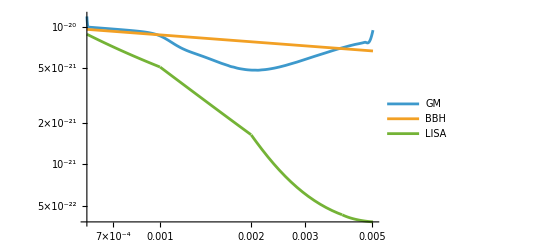

GM SNR: 12.3162

BBH SNR: 12.721

1799.85

```mathematica
Plot[{hcGM[fdet,CurrentDL],hcBBH[fdet,CurrentDL],(fdet*SnLISAdefault[fdet])^(1/2)},{fdet,fmin,fmax},ScalingFunctions->{"Log","Log"},PlotLegends->{"GM","BBH","LISA"}]
SNRGM[fdetmin_,fdetmax_,DL_]:=√NIntegrate[hcGM[f,DL]^2/(f*SnLISAdefault[f])*1/f,{f,fdetmin,fdetmax}]
SNRBBH[fdetmin_,fdetmax_,DL_]:=√NIntegrate[hcBBH[f,DL]^2/(f*SnLISAdefault[f])*1/f,{f,fdetmin,fdetmax}]
tc[Mc_,fgw0_]:=(5 c0^5)/(256 fgw0^(8/3) (G0 Mc)^(5/3) π^(8/3));(*注意这里fgw是source frame!*)
Print["GM SNR: ",SNRGM[fmin,fmax,CurrentDL]]
Print["BBH SNR: ",SNRBBH[fmin,fmax,CurrentDL]]
yr=31536000;
Print[(tc[Mchirp*Mpl,fmin(1+z0)]-tc[Mchirp*Mpl,fmax(1+z0)])/yr]
```

```mathematica
fgwRdet[R_,Mtot_,z_]:=1/(π(1+z))*√((G0*Mtot)/R^3);
fgwdetMax=fgwRdet[10Rb1*Lpl/.{M1->M,α1->α},(1+q+Mc/M1)M*Mpl,z0]
Print["tc(yr): ",tc[Mchirp*Mpl,(1+z0)fgwdetMax]/31536000]
Tinit=tc[Mchirp*Mpl,(1+z0)fgwdetMax]+10*31536000
fgwdetMin=((5 c0^5)/(256 Tinit (G0 Mchirp*Mpl)^(5/3) π^(8/3)))^(3/8)/(1+z0)
Print["BBH SNR 10yr: ",SNRBBH[fgwdetMin,fgwdetMax,CurrentDL]]
```

0.00425148

tc(yr): 8.65615

5.8834×10^8

0.00318771

BBH SNR 10yr: 8.11198

```mathematica
SNRBBHRange[M_(*Ms as unit 1*),q_,z_,DL_(*SI*),Rmin_(*SI*),Tobs_(*yr as unit 1*),SnLISA_]:=Module[{Ms,yr,c0,G0,Mtot,Mchirp,hcBBH,SNRBBH,tc,fgwRdet,Tinit,fgwdetMax,fgwdetMin},
Ms=1.989*10^30;
yr=31536000;
c0=299792458;(*m/s*)
G0=6.67*10^-11;(*N m^2/kg^2*)
Mtot=(1+q)M*Ms;
Mchirp=q^(3/5)/(1+q)^(1/5)M*Ms;
fgwRdet[R_]:=1/(π(1+z))*√((G0*Mtot)/R^3);
hcBBH[fdet_]:=√(2/(π^2 DL^2)*π^(2/3)/(3 c0^3)((1+z)G0*Mchirp)^(5/3)(fdet)^(-1/3));
SNRBBH[fdetmin_,fdetmax_]:=√NIntegrate[hcBBH[f]^2/(f*SnLISA[f])*1/f,{f,fdetmin,fdetmax}];
tc[Mc_,fgw0_]:=(5 c0^5)/(256 fgw0^(8/3) (G0 Mc)^(5/3) π^(8/3));(*fgw0是source frame*)
fgwdetMax=fgwRdet[Rmin];
Tinit=tc[Mchirp,(1+z)fgwdetMax]+Tobs*yr;
fgwdetMin=((5 c0^5)/(256 Tinit (G0 Mchirp)^(5/3) π^(8/3)))^(3/8)/(1+z);
SNRBBH[fgwdetMin,fgwdetMax]

]
SNRBBHParam[M_(*Ms as unit 1*),α_,q_,z_,DL_(*SI*),Rmin_(*Rb1 as unit 1*),Tobs_(*yr as unit 1*),SnLISA_]:=Module[{Ms,c0,G0,Rb1},
Ms=1.989*10^30;
c0=299792458;(*m/s*)
G0=6.67*10^-11;(*N m^2/kg^2*)
Rb1=(G0*M*Ms)/(c0^2 α^2);
SNRBBHRange[M,q,z,DL,Rmin*Rb1,Tobs,SnLISA]
]

Print[SNRBBHRange[M/Ms,q,z0,CurrentDL*Lpl,10Rb1*Lpl/.{M1->M,α1->α},10,SnLISAdefault]]
Print[SNRBBHParam[40,α,q,z0,CurrentDL*Lpl,10,10,SnLISAdefault]]
(*RegionPlot[SNRBBHParam[M,α,q,z0,CurrentDL*Lpl,10,10,SnLISAdefault]>=8,{M,40,100},{α,0.0,0.15}]*)
```

7.79701

4.59687

```mathematica
H0=70*10^3;(*m/s/Mpc*)
G=6.674*10^-11;(*SI*)
Msun=1.989*10^30; (*kg*)
yr=31536000; (* 1 year in seconds *)
day=3600*24; (*s*)
pc=3.086*10^16; (* 1 pc in metre *)
AU=1.496*10^11;  (* 1 AU in metre *)
c=299792458; (* the speed of light in astro. units *)
Ωm=0.315;
ΩΛ=0.685;
fgw[t_,Mc_,fgw0_]:=1/π(5/256 1/((5 c^5)/(256 fgw0^(8/3) (G Mc)^(5/3) π^(8/3))-t))^(3/8)((G Mc)/c^3)^(-5/8);
tc[Mc_,fgw0_]:=(5 c^5)/(256 fgw0^(8/3) (G Mc)^(5/3) π^(8/3));
DL[z_]:=10^6*pc*(1+z)c∫_0^z 1/(H0 √(Ωm(1+x)^3+ΩΛ))ⅆx;
Amp[f_,Mc_,dL_]:=√(5/(24 π^(4/3)))c/dL((G Mc)/c^3)^(5/6)1/f^(7/6);
Ψ[f_,MC_,ϕc_,tc_,fgw0_]:=2π f tc-ϕc-π/4+3/128(π G MC f/c^3)^(-5/3);
hf[f_,MC_,ϕc_,tc_,DL_,fgw0_]:=Amp[f,MC,DL] ⅇ^(ⅈ Ψ[f,MC,ϕc,tc,fgw0]);
dhfdM[f_,MC_,ϕc_,tc_,DL_,fgw0_]:=Evaluate[D[hf[f,MC,ϕc,tc,DL,fgw0],MC]];
ΓMM[MC_,ϕc_,tc_,DL_,fgw0_,fmax_]:=4 NIntegrate[Abs[dhfdM[f,MC,ϕc,tc,DL,fgw0]]^2/SnLISAdefault[f],{f,fgw0,fmax}]
M=40Msun;
Mchirp=(M*M)^(3/5)/(M+M)^(1/5);

Symbols={MC,ϕc,TC,Dl};
dhfdSym[f_,MC_,ϕc_,TC_,Dl_,fgw0_]=Table[D[hf[f,MC,ϕc,TC,Dl,fgw0],Symbols[[i]]],{i,1,Length[Symbols]}];
Γ[MC_,ϕc_,tc_,DL_,fgw0_,fmax_]:=Module[{Gamma},
Gamma=Table[0,{Length[Symbols]},{Length[Symbols]}];
For[i=1,i<=Length[Symbols],i++,
For[j=i,j<=Length[Symbols],j++,
Gamma[[i,j]]=Re[4 NIntegrate[Re[dhfdSym[f,MC,ϕc,tc,DL,fgw0][[i]]*Conjugate[dhfdSym[f,MC,ϕc,tc,DL,fgw0][[j]]]]/SnLISAdefault[f],{f,fgw0,fmax}]];
Gamma[[j,i]]=Gamma[[i,j]];
];
];
Gamma
]
fmin=0.0001;
fmax=0.1;
z0=0.5;
Γ[Mchirp,0,tc[Mchirp,fmin],DL[z0],fmin,fmax]//MatrixForm
Inverse[Γ[Mchirp,0,tc[Mchirp,fmin],DL[z0],fmin,fmax]]//MatrixForm
√(ΓMM[Mchirp,0,tc[Mchirp,fmin],DL[z0],fmin,fmax]^-1)/Mchirp
(Γ[Mchirp,0,tc[Mchirp,fmin],DL[z0],fmin,fmax][[1,1]])^-0.5/Mchirp(*相对误差，考虑四个量的测量（矩阵病态）*)
```

(1.48997×10^-45 | 8.18344×10^-23 | -1.89921×10^-24 | -7.88321×10^-57
8.18344×10^-23 | 56.9857 | -2.43348 | 0.
-1.89921×10^-24 | -2.43348 | 0.159506 | 0.
-7.88321×10^-57 | 0. | 0. | 7.53322×10^-51)

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.48997×10^-45,8.18344×10^-23,-1.89921×10^-24,-7.88321×10^-57},{8.18344×10^-23,56.9857,-2.43348,0.},{-1.89921×10^-24,-2.43348,0.159506,0.},{-7.88321×10^-57,0.,0.,7.53322×10^-51}} may contain significant numerical errors.

(7.5377×10^44 | -2.00626×10^21 | -2.16331×10^22 | 7.8879×10^38
-2.00626×10^21 | 0.055693 | 0.825782 | -2.09947×10^15
-2.16331×10^22 | 0.825782 | 18.6102 | -2.26382×10^16
7.8879×10^38 | -2.09947×10^15 | -2.26382×10^16 | 1.32745×10^50)

3.74044×10^-10

3.74044×10^-10

```mathematica
fgw[t_,MC_,fgw0_]:=1/π(5/256 1/(5/(256 fgw0^(8/3) MC^(5/3) π^(8/3))-t))^(3/8)MC^(-5/8);
tc[MC_,fgw0_]:=5/(256 fgw0^(8/3) MC^(5/3) π^(8/3));
DL[z_]:=10^6*pc/Lpl*(1+z)c0∫_0^z 1/(H0 √(Ωm(1+x)^3+ΩΛ))ⅆx;(*Natrual unit*)
Amp[f_,MC_,DL_]:=√(5/(24 π^(4/3)))1/DL MC^(5/6)1/f^(7/6);
Ψ[f_,MC_,ϕc_,tc_,fgw0_]:=2π f tc-ϕc-π/4+3/128(π MC f)^(-5/3);
hf[f_,MC_,ϕc_,tc_,DL_,fgw0_]:=Amp[f,MC,DL] ⅇ^(ⅈ Ψ[f,MC,ϕc,tc,fgw0]);
dhfdM[f_,MC_,ϕc_,tc_,DL_,fgw0_]:=Evaluate[D[hf[f,MC,ϕc,tc,DL,fgw0],MC]];
ΓMM[MC_,ϕc_,tc_,DL_,fgw0_,fmax_]:=4 NIntegrate[Abs[dhfdM[f,MC,ϕc,tc,DL,fgw0]]^2/(SnLISAdefault[f/Tpl]*Tpl),{f,fgw0*Tpl,fmax*Tpl}]
Symbols={MC,ϕc,TC,Dl};
dhfdSym[f_,MC_,ϕc_,TC_,Dl_,fgw0_]=Table[D[hf[f,MC,ϕc,TC,Dl,fgw0],Symbols[[i]]],{i,1,Length[Symbols]}];
Γ[MC_,ϕc_,tc_,DL_,fgw0_,fmax_]:=Module[{Gamma},
Gamma=Table[0,{Length[Symbols]},{Length[Symbols]}];
For[i=1,i<=Length[Symbols],i++,
For[j=i,j<=Length[Symbols],j++,
Gamma[[i,j]]=Re[4 NIntegrate[Re[dhfdSym[f,MC,ϕc,tc,DL,fgw0][[i]]*Conjugate[dhfdSym[f,MC,ϕc,tc,DL,fgw0][[j]]]]/(SnLISAdefault[f/Tpl]*Tpl),{f,fgw0*Tpl,fmax*Tpl}]];
Gamma[[j,i]]=Gamma[[i,j]];
];
];
Gamma
]
Γ[Mchirp,0,tc[Mchirp,fmin*Tpl],DL[z0],fmin,fmax]//MatrixForm
Inverse[Γ[Mchirp,0,tc[Mchirp,fmin*Tpl],DL[z0],fmin,fmax]]//MatrixForm
(Inverse[Γ[Mchirp,0,tc[Mchirp,fmin*Tpl],DL[z0],fmin,fmax]][[1,1]])^0.5/Mchirp(*相对误差，考虑四个量的测量（矩阵病态）*)
√(ΓMM[Mchirp,0,tc[Mchirp,fmin*Tpl],DL[z0],fmin,fmax]^-1)/Mchirp(*相对误差，只考虑M*)
```

General::munfl: 1/((1.85529×10^43)^7.5) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((1.85529×10^43)^20) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((1.85529×10^43)^8.8) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in f near {f} = {4.9952×10^-46}. NIntegrate obtained -6.52574×10^-16+0. ⅈ and 1.89364×10^-15 for the integral and error estimates.

(3.11446×10^54 | 3.25405×10^64 | -3.90425×10^19 | -2.6103×10^-15
3.25405×10^64 | 3.55771×10^75 | -7.87139×10^30 | 0.
-3.90425×10^19 | -7.87139×10^30 | 2.7262×10^-14 | 0.
-2.6103×10^-15 | 0. | 0. | 1.2282×10^-46)

General::munfl: 1/((1.85529×10^43)^7.5) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((1.85529×10^43)^20) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((1.85529×10^43)^8.8) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in f near {f} = {4.9952×10^-46}. NIntegrate obtained -6.52574×10^-16+0. ⅈ and 1.89364×10^-15 for the integral and error estimates.

Inverse::luc: Result for Inverse of badly conditioned matrix {{3.11446×10^54,3.25405×10^64,-3.90425×10^19,-2.6103×10^-15},{3.25405×10^64,3.55771×10^75,-7.87139×10^30,0.},{-3.90425×10^19,-7.87139×10^30,2.7262×10^-14,0.},{-2.6103×10^-15,0.,0.,1.2282×10^-46}} may contain significant numerical errors.

(3.69474×10^-55 | -6.11512×10^-66 | -1.2365×10^-21 | 7.85246×10^-24
-6.11512×10^-66 | 8.79426×10^-76 | 2.45161×10^-31 | -1.29965×10^-34
-1.2365×10^-21 | 2.45161×10^-31 | 1.05696×10^14 | -2.62793×10^10
7.85246×10^-24 | -1.29965×10^-34 | -2.62793×10^10 | 8.14201×10^45)

General::munfl: 1/((1.85529×10^43)^7.5) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((1.85529×10^43)^20) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((1.85529×10^43)^8.8) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in f near {f} = {4.9952×10^-46}. NIntegrate obtained -6.52574×10^-16+0. ⅈ and 1.89364×10^-15 for the integral and error estimates.

Inverse::luc: Result for Inverse of badly conditioned matrix {{3.11446×10^54,3.25405×10^64,-3.90425×10^19,-2.6103×10^-15},{3.25405×10^64,3.55771×10^75,-7.87139×10^30,0.},{-3.90425×10^19,-7.87139×10^30,2.7262×10^-14,0.},{-2.6103×10^-15,0.,0.,1.2282×10^-46}} may contain significant numerical errors.

8.77613×10^-60

General::munfl: 1/((1.85529×10^43)^7.5) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((1.85529×10^43)^20) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((1.85529×10^43)^8.8) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

8.18125×10^-60

```mathematica
Mpl=2.176*10^-8;

(* 天文单位转换 *)
Mpc = 3.08567758*10^22/Lpl;  (* 1 Mpc in Planck lengths *)
Msun = 1.98855*10^30/Mpl;    (* 1 Solar mass in Planck masses *)
yr = 3.1556952*10^7/Tpl;     (* 1 year in Planck times *)

(* 宇宙学参数 *)
H0 = 70*1000/(10^6*pc)*Tpl;  (* 70 km/s/Mpc in natural units *)
Ωm = 0.315;
ΩΛ = 0.685;

(* 引力波频率演化 *)
fgw[t_, MC_, fgw0_] := 
  1/π (5/256 1/((5/(256 fgw0^(8/3) MC^(5/3) π^(8/3)) - t)))^(3/8) MC^(-5/8);

(* 合并时间 *)
tc[MC_, fgw0_] := 5/(256 fgw0^(8/3) MC^(5/3) π^(8/3));

(* 光度距离 *)
DL[z_] := Mpc*(1 + z)/H0* ∫_0^z 1/(√(Ωm(1+x)^3+ΩΛ))ⅆx;

(* 引力波振幅 *)
Amp[f_, MC_, DL_] := Sqrt[5/(24 π^(4/3))] 1/DL MC^(5/6) 1/f^(7/6);

(* 引力波相位 *)
Ψ[f_, MC_, ϕc_, tc_, fgw0_] := 
  2 π f tc - ϕc - π/4 + 3/128 (π MC f)^(-5/3);

(* 引力波应变 *)
hf[f_, MC_, ϕc_, tc_, DL_, fgw0_] := 
  Amp[f, MC, DL] E^(I Ψ[f, MC, ϕc, tc, fgw0]);

(* 对chirp质量的导数 *)
dhfdM[f_, MC_, ϕc_, tc_, DL_, fgw0_] := 
  Evaluate[D[hf[f, MC, ϕc, tc, DL, fgw0], MC]];

(* 质量参数的Fisher矩阵元素 *)
ΓMM[MC_, ϕc_, tc_, DL_, fgw0_, fmax_] := 
 4 NIntegrate[
   Abs[dhfdM[f, MC, ϕc, tc, DL, fgw0]]^2/(SnLISAdefault[f/Tpl]/Tpl), 
   {f, fgw0, fmax}]

(* 所有参数的导数 *)
Symbols = {MC, ϕc, TC, Dl};
dhfdSym[f_, MC_, ϕc_, TC_, Dl_, fgw0_] = 
  Table[D[hf[f, MC, ϕc, TC, Dl, fgw0], Symbols[[i]]], {i, 1, Length[Symbols]}];

(* 完整的Fisher信息矩阵 *)
Γ[MC_, ϕc_, tc_, DL_, fgw0_, fmax_] := 
 Module[{Gamma},
  Gamma = Table[0, {Length[Symbols]}, {Length[Symbols]}];
  For[i = 1, i <= Length[Symbols], i++,
   For[j = i, j <= Length[Symbols], j++,
     Gamma[[i, j]] = 
      Re[4 NIntegrate[
         Re[dhfdSym[f, MC, ϕc, tc, DL, fgw0][[i]]*
           Conjugate[dhfdSym[f, MC, ϕc, tc, DL, fgw0][[j]]]]/(SnLISAdefault[f/Tpl]/Tpl), 
         {f, fgw0, fmax}]];
     Gamma[[j, i]] = Gamma[[i, j]];
     ];
   ];
  Gamma
  ]

(* 参数设置和计算 *)
M = 40 Msun;  (* 每个黑洞质量 *)
Mchirp = (M*M)^(3/5)/(M + M)^(1/5);  (* chirp质量 *)
fmin = 0.0001; (*SI*)
fmax = 0.1; (*SI*)
z0 = 0.5;       (* 红移 *)

fminnat = fmin * Tpl;
fmaxnat = fmax * Tpl;

(* 计算Fisher矩阵 *)
√(ΓMM[Mchirp,0,tc[Mchirp,fminnat],DL[z0],fminnat,fmaxnat]^-1)/Mchirp
```

General::munfl: 1/((1.85529×10^43)^7.5) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((1.85529×10^43)^20) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((1.85529×10^43)^8.8) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

7.03679×10^47

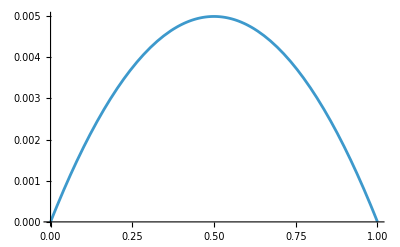

```mathematica
Plot[(((1+(1-y)b)(x+y b))/(x+b))^(3/5)-1/.{b->0.2,x->1},{y,0,1}]
```

```mathematica
-(b (2+b^3-2 b^2 x-2 x^2+b (-3+2 x+x^2)))/(4 (b+x))/.{b->0.1,x->1}
```

0.000431818

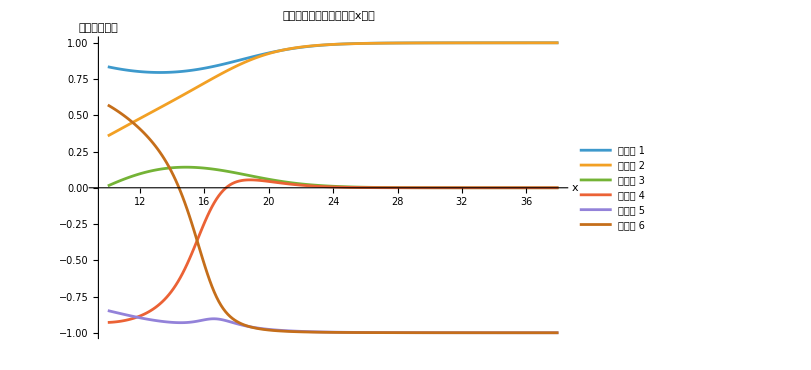

```mathematica
baseAngularMomenta={0,-1,1,0,-1,1};
totalAngularMomenta=Table[(*获取当前x点对应的6个本征矢量，每个是6维系数*)eigenvecs=eigenvectors[[i]];(*形状 (6,6)*)(*对每个本征矢量计算角动量期望值*)angularMomentumExpectations=Table[coeffs=eigenvecs[[j]];(*第j个本征矢量的6个系数*)probabilities=Abs[coeffs]^2;(*概率= |系数|^2*)(*计算期望值：概率点乘角动量*)probabilities.baseAngularMomenta,{j,1,6}];
(*返回6个本征态对应的角动量期望值*)angularMomentumExpectations
,{i,1,Length[xValues]}];
(*在同一图中绘制所有本征态*)ListPlot[Table[Transpose[{xValues,totalAngularMomenta[[All,i]]}],{i,1,6}],PlotLabel->"各本征态角动量期望值随x变化",AxesLabel->{"x","角动量期望值"},PlotRange->All,PlotLegends->Table["本征态 "<>ToString[i],{i,1,6}],Joined->True,ImageSize->600]
```

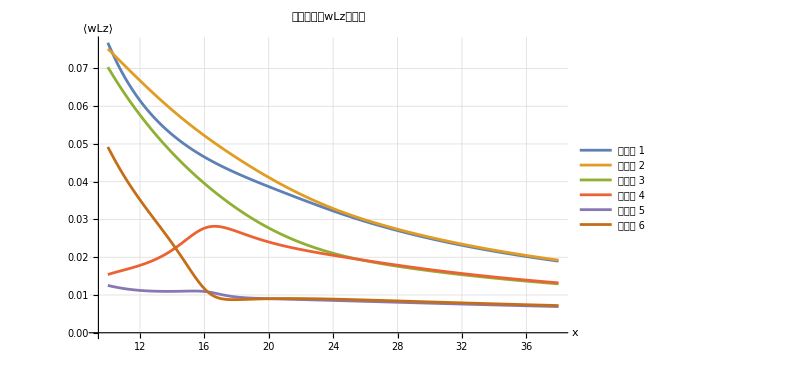

```mathematica
(*假设数据已加载*)(*eigenvectors:shape (200,6,6) 数组，每个位置的本征矢量*)(*wLz:shape (200,6,6) 数组，每个位置的wLz矩阵元*)(*xValues:长度200的数组*)(*计算每个本征态的wLz期望值*)wLzExpectations=Table[(*获取当前x点的数据*)currentEigenvecs=eigenvectors[[k]];(*形状 (6,6)*)currentWlz=DimlessωLz[[k]];(*形状 (6,6)*)(*计算6个本征态的期望值*)Table[(*获取第n个本征矢量*)psi=currentEigenvecs[[n]];(*长度为6的向量*)(*方法1:直接计算<psi|wLz|psi> =psi^†.wLz.psi*)(*注意：Mathematica默认向量是列向量，但这里是一维列表*)expectation=Conjugate[psi].currentWlz.psi;
(*确保结果是实数，因为wLz应该是厄米矩阵*)Re[expectation],{n,1,6}],{k,1,Length[xValues]}];

BaseFreq=1/π Sqrt[(M1+M2+Mc)/(xValues^3*Rb1^3)]/.{M1->M,α1->α,Q->q};
CorrectwLzExpectations=Table[Table[wLzExpectations[[i,j]]/BaseFreq[[i]]*Sqrt[GWFreqSquare[[j,i]]],{j,1,6}],{i,1,Num}];

(*绘制所有本征态的wLz期望值*)
ListPlot[Table[Transpose[{xValues,CorrectwLzExpectations[[All,i]]}],{i,1,6}],PlotLabel->"各本征态的wLz期望值",AxesLabel->{"x",Style["⟨wLz⟩",Italic]},PlotRange->All,PlotLegends->Table["本征态 "<>ToString[i],{i,1,6}],Joined->True,PlotStyle->ColorData[97]/@Range[6],ImageSize->600,GridLines->Automatic]
```